```mathematica
link=Install[LinkConnect[" 33455@192.168.150.130,45143@192.168.150.130",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle = With[
{c=15,Ωp=1.0,Ωe=-100,θr=0.45,θe=Sqrt[0.8],θb=0.045,ωb=14.2302,ωe=150,
ωp ={0.0266,
0.1207,
0.3312,
0.5934,
0.8158,
0.9859,
1.1178,
1.2203,
1.2975,
1.3516,
1.3836,
1.3943,
1.3836,
1.3516,
1.2975,
1.2203,
1.1178,
0.9859,
0.8158,
0.5934,
0.3312,
0.1207,
0.0266},
vd={1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591,-1.0125,-1.30164,-1.55124,-1.7537,-1.90288,-1.99424,-2.025,-1.99424,-1.90288},
vr={-0.692591,-0.351638,0,0.351638,0.692591,1.0125,1.30164,1.55124,1.7537,1.90288,1.99424,2.025,1.99424,1.90288,1.7537,1.55124,1.30164,1.0125,0.692591,0.351638,0,-0.351638,-0.692591}
},
dist=Join[
Thread[wstpDRingDistribution[Ωp,ωp,θr,θr,vd*2.25/2.025,vr*2.25/2.025]],
Thread[wstpDMaxwellianDistribution[{Ωp,Ωe},{ωb,ωe},{θb,θe}]]];
wstpDCreateDispersionObject[c,dist]];
```

```mathematica
r=Complex[2.0,0.03];
check=With[{k=2.3,wna=88.6Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],r(1+0.0001 I {0,1,2}),MaxIterations->100]];
```

{4.60664-0.0126111 ⅈ,4.6106-0.00608713 ⅈ,4.63063+0.00807953 ⅈ,4.68484+0.0216979 ⅈ,4.69807+0.0197803 ⅈ,4.76368+0.0185738 ⅈ}

{4.60664-0.0126111 ⅈ,4.6106-0.00608713 ⅈ,4.63063+0.00807953 ⅈ,4.68484+0.0216979 ⅈ,4.69807+0.0197803 ⅈ,4.76368+0.0185738 ⅈ,4.78867+0.0158618 ⅈ,4.83838+0.0134117 ⅈ,4.88895+0.0116628 ⅈ,4.94119+0.0108577 ⅈ,5.00151+0.00981307 ⅈ,5.038+0.00955489 ⅈ,5.08861+0.010088 ⅈ,5.13009+0.00782628 ⅈ,5.17239+0.00368376 ⅈ,5.21282-0.00638195 ⅈ,5.25215-0.0284651 ⅈ,5.27695-0.0901136 ⅈ,5.26902-0.117647 ⅈ,5.26033-0.130243 ⅈ,5.2509-0.147558 ⅈ,5.24133-0.161958 ⅈ,5.23148-0.177754 ⅈ,5.22179-0.188619 ⅈ,5.21203-0.19865 ⅈ,5.20491-0.207468 ⅈ}

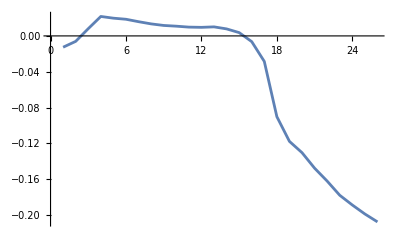

```mathematica
sol1=With[{k=Range[6.0,5.5,-0.1],wna=87.6Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[4.7,0.03] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol2=With[{k=Range[6.1,8.0,0.1],wna=87.6Degree},wstpDFindRoot[handle,k Cos[wna],k Sin[wna],Complex[4.7,0.03] (1+0.0001 I {0,1,2}),MaxIterations->100]];
sol1=Reverse[sol1[[2,2]]]
sol=Join[sol1,sol2[[2,2]]]
ListLinePlot[Im[sol]]
```

```mathematica
Export["vs=2.25-88.4-0.9h-0.045-im-5,6.0-8.0.csv",Im[sol]];
Export["vs=2.25-88.4-0.9h-0.045-re-5,6.0-8.0.csv",Re[sol]];
```

```mathematica
r=Complex[2.0,0.05] ;
dk=0.01;
kl=1.8;
kmid=2.2;
kr=3.0;
dwna=0.05Degree;
wnai=86.8Degree;
wnamid=88Degree;
wnaf=89.5Degree;
a2={};
With[{k=Range[kmid,kl,-dk]},Do[sol=wstpDFindRoot[handle,k Cos[wna],k Sin[wna],r(1+0.0001 I {0,1,2}),MaxIterations->100];
a2=Append[a2,Im[sol[[2,2]]]],{wna,wnamid,wnaf,dwna}]];
a1={};
With[{k=Range[kmid+dk,kr,dk]},Do[sol=wstpDFindRoot[handle,k Cos[wna],k Sin[wna],r (1+0.0001 I {0,1,2}),MaxIterations->100];
a1=Append[a1,Im[sol[[2,2]]]],{wna,wnamid,wnaf,dwna}]];
a3={};
With[{k=Range[kmid,kl,-dk]},Do[sol=wstpDFindRoot[handle,k Cos[wna],k Sin[wna],r (1+0.0001 I {0,1,2}),MaxIterations->100];
a3=Append[a3,Im[sol[[2,2]]]],{wna,wnamid-dwna,wnai,-dwna}]];
a4={};
With[{k=Range[kmid+dk,kr,dk]},Do[sol=wstpDFindRoot[handle,k Cos[wna],k Sin[wna],r(1+0.0001 I {0,1,2}),MaxIterations->100];
a4=Append[a4,Im[sol[[2,2]]]],{wna,wnamid-dwna,wnai,-dwna}]];
```

```mathematica
ra2=Map[Reverse,a2];
a1;
toup=Join[ra2,a1,2];
ra3=Map[Reverse,a3];
a4;
todown=Join[ra3,a4,2];
rtodown=Reverse[todown];
```

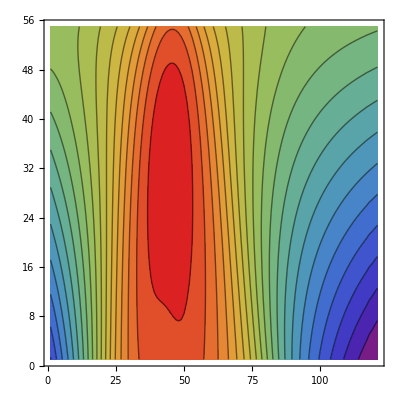

0.0684075

```mathematica
total=Join[rtodown,toup];
 ListContourPlot[total,ColorFunction->"Rainbow",Contours->20]
Export["vs=2.25-0.9h-0.045-2.8-3.0,86.8-89.5-.csv",total];
Max[total]
```